```mathematica
LaunchKernels[]
(*Needs["FourierSeries`"]*)
```

{KernelObject[1,local],KernelObject[2,local]}

```mathematica
(*константы*)
α=1/137;lc=SetPrecision[3.86 10^-11,MachinePrecision];cc=SetPrecision[3 10^(10),MachinePrecision];mee=SetPrecision[0.511 10^6,MachinePrecision];
(*параметры траектории*)
γ=SetPrecision[500,MachinePrecision];(*гамма-фактор заряженных частиц*)
λo=SetPrecision[40/25 10^(-3)/lc,MachinePrecision];(*период ондулятора 1 см*)
kdip=SetPrecision[0,MachinePrecision];(*параметр дипольности*)
βp=Sqrt[1-(1+kdip^2)/γ^2];(*составляющая скорости вдоль оси 3*)
ω=(2 π)/λo βp;(*круговая частота колебаний в частиц однуляторе*)
(*χt=1;(*χt -- киральность спирали траектории; γ=235, K=1.29,lambda_0=3.3cm -- SLAC, Hemsing*)*)
θi=0;(*угол падения частицы относительно нормали к поверхности*)
No=2;(*число периодов ондулятора*)
Lt=No 2 Pi/ω;(*время пролета ондулятора*)
mMax =10; (*ожидаемое максимальное значение m*)
Print["Магнитное поле в ондуляторе H (Гс): ",(2 Pi Sqrt[2]kdip/λo) 4.41 10^(13)]
```

Магнитное поле в ондуляторе H (Гс): 0.

```mathematica
Lz= βp Lt;(*толщина пластины холестерика*)
Nc=40;(*число периодов холестерика*)
qc=Pi Nc/Lz;(*волновой вектор холестерика*)
(*диэлектрическая проницаемость*)
(*ϵc[ω1_?NumberQ]:=SetPrecision[Module[{λ=2 Pi/ω1 lc 10^4},
If[λ≥0.275&&λ≤0.546,(1+0.014755297/(426.29740-λ^(-2)))^2,1]],90](*гелий*)*)
(*n=1.49669+0.00785λ^(−2)+0.00026λ^(−4)(*обыкновенная*)
n=1.4990+0.0072λ^(−2)+0.0003λ^(−4)*)
(*n=1.67798+0.01696λ^(−2)+0.00127λ^(−4)(*необыкновенная*)
n=1.6933+0.0078λ^(−2)+0.0028λ^(−4)*)
ϵpp[k0_]=SetPrecision[2.22,MachinePrecision];(*перпендикулярная диэлектрическая проницаемость*)
ϵpl[k0_]=SetPrecision[2.49,MachinePrecision];(*параллельная диэлектрическая проницаемость*)
dec[k0_]=(ϵpl[k0]-ϵpp[k0])/ϵpp[k0];(*анизотропия*)
Print["Волновой вектор холестерика q: ",qc mee, " эВ"]
Print["Толщина пластины холестерика Lz: ",Lz lc 10^4, " мкм"]
(*Print["Плазменная частота: ",ωp mee," эВ,  ",2.42 10^(14) ωp mee," Гц"]*)
Module[{xx=5/mee,yy=1/2},(*предполагаемая энергия фотона и npp*)
Print["Анизотропия de: ",dec[xx]];
Print["Параметр ВКБ: ", (dec[xx] ϵpp[xx]^(1/2) xx/(4 qc))^2];
Print["Период по энергии резонансов, np=",yy,": ",Pi mee/(Lz Sqrt[ϵpp[xx]-(yy)^2]),", ",Pi mee/(Lz 2/Pi Sqrt[1+dec[xx]] EllipticE[-dec[xx] (yy)^2/((1+dec[xx]) (ϵpp[xx]-(yy)^2))] Sqrt[ϵpp[xx]-(yy)^2]),", ",Pi/2 mee/(Lz (Sqrt[ϵpp[xx]-(yy)^2]-2/Pi Sqrt[1+dec[xx]] EllipticE[-dec[xx] (yy)^2/((1+dec[xx]) (ϵpp[xx]-(yy)^2))] Sqrt[ϵpp[xx]-(yy)^2]))," эВ"]]
```

Волновой вектор холестерика q: 0.774583 эВ

Толщина пластины холестерика Lz: 32. мкм

Анизотропия de: 0.121622

Параметр ВКБ: 0.0855182

Период по энергии резонансов, np=1/2: 0.0137967, 0.0129827, -0.110021 эВ

```mathematica
e3={0,0,1};
e1={1,0,0};
e2={0,1,0};
ep=e1+ⅈ e2;
em=e1-ⅈ e2;
```

```mathematica
(*xoa=kdip/(Sqrt[2] ω γ);yoa=xoa;(*амплитуды колебаний*)*)
zo=-Lz;(*начальная координата в компотоновский длинах волн. частица вылетает из пластины в сторону детектора*)
(*xo=0;yo=0;zo=0;начальные координаты в компотоновский длинах волн*)
(*ωs=χt ω;(*частота со знаком*)*)
vx0=Sin[θi] Sqrt[1-1/γ^2];vy0=0;vz0=Cos[θi] Sqrt[1-1/γ^2];(*скорость влета*)
rt[t_]={0,0,zo+βp t};
v[t_]={0,0,βp};
xo=rt[0][[1]];yo=rt[0][[2]];
```

```mathematica
tfin=Lt;
```

```mathematica
rf=rt[tfin];
vxf=0;vyf=0;vzf=Sqrt[1-1/γ^2];(*вылетает вдоль оси -- нормали к пластине*)
```

```mathematica
xp[t_]=rt[t].ep;
xm[t_]=rt[t].em;
x3[t_]=rt[t].e3;
x0[t_]=t;  (*c=1*)
vp[t_]=v[t].ep;
vm[t_]=v[t].em;
v3[t_]=v[t].e3;
```

```mathematica
k31[k0s_,kp_,de_]=(√((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))/(√2)+1+(kp^2 (-(4 (√(k0s (de (de k0s+8)+16))+4))-de (de k0s+√(k0s (de (de k0s+8)+16))+4)))/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)));(*правая быстрая ветвь при q=1*)
k32[k0s_,kp_,de_]=√((de k0s)/2-1/2 √(k0s (de (de k0s+8)+16))+k0s+1)+1+(-de (-de k0s+√(k0s (de (de k0s+8)+16))-4)-4 √(k0s (de (de k0s+8)+16))+16)/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))) kp^2;(*правая медленная ветвь при q=1*)
```

```mathematica
Clear[CoeffLinComb]
```

```mathematica
CoeffLinComb[s_/;(s^2==1),k00_?NumberQ,k0_?NumberQ,k0s_?NumberQ,kp_?NumberQ,ϕ_?NumberQ,rff_?NumberQ,n3_?NumberQ,k3b_?NumberQ,de_?NumberQ,pf_?NumberQ,ps_?NumberQ]:=Module[{xps0,xmsm2,xps2,xms0,xpsm2,xmsm4,yps0,ymsm2,yps2,yms0,ypsm2,ymsm4,xms2,xpsm4,yms2,ypsm4,tf,ts,r,apfs,amfs,apss,amss,amfcs,apfcs,amscs,apscs,rapfs,ramfs,rapss,ramss,ramfcs,rapfcs,ramscs,rapscs,n3i,um,h0i,t0l,tfl,tsl,tpi,tm,gv,ach,al,norm},

n3i=1/n3;

xps0=1;
xmsm2=-(2 (-((√((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))/(√2)+1)^2+(de k0s)/2+k0s))/(de k0s)+kp^2 ((√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4)/(2 de k0s^2)-(2 (((4 (√(k0s (de (de k0s+8)+16))+4)+de (de k0s+√(k0s (de (de k0s+8)+16))+4)) (√2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+2))/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)))-de/4-1))/(de k0s));
xps2=-kp^2 ((de (de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))+8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xms0=-kp^2 (((de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4) (√(k0s (de (de k0s+8)+16))+6 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+20))/(16 k0s (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))+8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xpsm2=-kp^2 (((√(k0s (de (de k0s+8)+16))-6 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+20) (de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 k0s (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))-8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xmsm4=-kp^2 ((de(de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))-8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));

(*медленная волна*)
yps0=1;
ymsm2=-(2 (-1/4 (√(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+2)^2+(de k0s)/2+k0s))/(de k0s)+(kp^2 (k0s (-(√2 de^2 k0s)+√2 de √(k0s (de (de k0s+8)+16))-4 de √((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)-4 √2 (3 de+4))+4 (√2 √(k0s (de (de k0s+8)+16))+√(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)))))/(2 de k0s^2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)));
yps2=kp^2 (de (de k0s-√(k0s (de (de k0s+8)+16))+2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+4))/(16 (-(4 (de+2) k0s)+6 √(k0s (de (de k0s+8)+16))-8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))-16));
yms0=-kp^2 (((√(k0s (de (de k0s+8)+16))-6 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-20) (-(de k0s)+√(k0s (de (de k0s+8)+16))-2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-4))/(16 k0s (4 (de+2) k0s-6 √(k0s (de (de k0s+8)+16))+8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))+16)));
ypsm2=-kp^2 (((-(de k0s)+√(k0s (de (de k0s+8)+16))-2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-4) (√(k0s (de (de k0s+8)+16))+6 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-20))/(16 k0s (4 (de+2) k0s-6 √(k0s (de (de k0s+8)+16))-8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))+16)));
ymsm4=kp^2 (de (de k0s-√(k0s (de (de k0s+8)+16))+2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+4))/(16 (-(4 (de+2) k0s)+6 √(k0s (de (de k0s+8)+16))+8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))-16));

xmsm2=If[xmsm2∈Reals,xmsm2,0];(*коэффициенты должны быть вещественными*)
xps2=If[xps2∈Reals,xps2,0];
xms0=If[xms0∈Reals,xms0,0];
xpsm2=If[xpsm2∈Reals,xpsm2,0];
xmsm4=If[xmsm4∈Reals,xmsm4,0];
ymsm2=If[ymsm2∈Reals,ymsm2,0];(*коэффициенты должны быть вещественными*)
yps2=If[yps2∈Reals,yps2,0];
yms0=If[yms0∈Reals,yms0,0];
ypsm2=If[ypsm2∈Reals,ypsm2,0];
ymsm4=If[ymsm4∈Reals,ymsm4,0];

xms2=0;xpsm4=0;yms2=0;ypsm4=0;(*зануляем высшие поправки*)

tf=Exp[-I pf ϕ]; ts=Exp[-I ps ϕ]; r=1/rff^2;(*фазовые множители*)
t0l=Exp[-I k00 n3 Lz];tfl=Exp[-I pf qc Lz];tsl=Exp[-I ps qc Lz];

apfs=tf (xps0+xps2 r+xpsm2/r);(*a_pm при z=0*)
amfs=tf(xms0+xmsm2/r+xmsm4/r^2);
apss=ts(yps0+yps2 r+ypsm2/r);
amss=ts (yms0+ymsm2/r+ymsm4/r^2);
amfcs=1/tf (xps0+xps2/r+xpsm2 r);(*a_pm сопряженное при z=0*)
apfcs=1/tf (xms0+xmsm2 r+r^2xmsm4);
amscs=1/ts (yps0 +yps2/r+ypsm2 r);
apscs=1/ts(yms0+ymsm2 r+ymsm4 r^2);
(*-I K dz U11 при z=0*)
rapfs=tf (pf (xps0+kp^2/(2 k3b^2) (xps0+xms0))+(pf+2) r (xps2+kp^2/(2 k3b^2) (xps2+xms2))+(pf-2)/r (xpsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2)));
ramfs=tf (pf (xms0+kp^2/(2 k3b^2) (xps0+xms0))+(pf-2)/r (xmsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2))+(pf-4)/r^2 (xmsm4+kp^2/(2 k3b^2) (xpsm4+xmsm4)));
rapss=ts (ps (yps0+kp^2/(2 k3b^2) (yps0+yms0))+(ps+2) r (yps2+kp^2/(2 k3b^2) (yps2+yms2))+(ps-2)/r (ypsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2)));
ramss=ts (ps (yms0+kp^2/(2 k3b^2) (yps0+yms0))+(ps-2)/r (ymsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2))+(ps-4)/r^2 (ymsm4+kp^2/(2 k3b^2) (ypsm4+ymsm4)));
(*U21*)
ramfcs=-1/tf (pf (xps0+kp^2/(2 k3b^2) (xps0+xms0))+(pf+2)/r (xps2+kp^2/(2 k3b^2) (xps2+xms2))+(pf-2) r (xpsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2)));
rapfcs=-1/tf ((pf (xms0+kp^2/(2 k3b^2) (xps0+xms0))+(pf-2) r (xmsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2))+(pf-4) r^2 (xmsm4+kp^2/(2 k3b^2) (xpsm4+xmsm4))));
ramscs=-1/ts (ps (yps0+kp^2/(2 k3b^2) (yps0+yms0))+(ps+2)/r (yps2+kp^2/(2 k3b^2) (yps2+yms2))+(ps-2) r (ypsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2)));
rapscs=-1/ts (ps (yms0+kp^2/(2 k3b^2) (yps0+yms0))+(ps-2) r (ymsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2))+(ps-4) r^2 (ymsm4+kp^2/(2 k3b^2) (ypsm4+ymsm4)));

um={{apfs,apss,apfcs,apscs},{amfs,amss,amfcs,amscs},{rapfs,rapss,rapfcs,rapscs},{ramfs,ramss,ramfcs,ramscs}};
h0i={{(n3i-1)/(4 √2),(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)},{(n3i+1)/(4 √2),(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i+1)/(4 √2),-(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i-1)/(4 √2),-(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)}};
(*h0={{(n3-1)/(√2),(n3+1)/(√2),(-n3-1)/(√2),(1-n3)/(√2)},{(n3+1)/(√2),(n3-1)/(√2),(1-n3)/(√2),(-n3-1)/(√2)},{(k0 (1-n3))/(√2),(k0 (n3+1))/(√2),(k0 (n3+1))/(√2),(k0 (1-n3))/(√2)},{(k0 (n3+1))/(√2),(k0 (1-n3))/(√2),(k0 (1-n3))/(√2),(k0 (n3+1))/(√2)}};*)

tpi={{1/t0l,0,0,0},{0,1/t0l,0,0},{0,0,t0l,0},{0,0,0,t0l}};
tm={{tfl,0,0,0},{0,tsl,0,0},{0,0,1/tfl,0},{0,0,0,1/tsl}};

gv={(n3-s)/(√2),(n3+s)/(√2),(k0 (1-n3 s))/(√2),(k0 (n3 s+1))/(√2)};

ach=Inverse[um].gv;
(*ach=LinearSolve[um,gv];*)
al=tpi.h0i.um.tm.ach;
norm=Sqrt[2/(1+Conjugate[al].al)];
{norm,ach,al,{xmsm2,xps2,xms0,xpsm2,xmsm4},{ymsm2,yps2,yms0,ypsm2,ymsm4}}](*выдает ответ в виде списка*)
```

```mathematica
ModeFun1[tetb_?NumberQ,kp_?NumberQ,rff_?NumberQ,xmsm2_?NumberQ,xps2_?NumberQ,xms0_?NumberQ,xpsm2_?NumberQ,xmsm4_?NumberQ,pf_?NumberQ,k3b_?NumberQ,rf1_?NumberQ]:=Module[{xps0,xms2,xpsm4,tf,r,apfs,amfs,a3fs,amfcs,apfcs,a3fcs},
xps0=1;
xms2=0;xpsm4=0;(*зануляем высшие поправки*)

tf=Exp[I pf tetb];r=rf1;(*фазовые множители*)

apfs=tf (xps0+xps2 r+xpsm2/r);(*a_pm,3*)
amfs=tf(xms0+xmsm2/r+xmsm4/r^2);
a3fs=-kp/(2 k3b^2) tf ((pf xps0+(pf+2) xps2 r+(pf-2) xpsm2/r)+(pf xms0+(pf-2) xmsm2/r+(pf-4) xmsm4/r^2));
amfcs=1/tf (xps0+xps2/r+xpsm2 r);(*a_pm,3 сопряженное*)
apfcs=1/tf (xms0+xmsm2 r+r^2xmsm4);
a3fcs=kp/(2 k3b^2)/tf ((pf xps0+(pf+2) xps2/r+(pf-2) xpsm2 r)+(pf xms0+(pf-2) xmsm2 r+(pf-4) r^2xmsm4));

{{apfs rff,amfs/rff,a3fs},{apfcs rff,amfcs/rff,a3fcs}}](*ответ в виде списка без общего фазового множителя*)
```

```mathematica
ModeFun2[tetb_?NumberQ,kp_?NumberQ,rff_?NumberQ,ymsm2_?NumberQ,yps2_?NumberQ,yms0_?NumberQ,ypsm2_?NumberQ,ymsm4_?NumberQ,ps_?NumberQ,k3b_?NumberQ,rf1_?NumberQ]:=Module[{yps0,yms2,ypsm4,ts,r,apss,amss,a3ss,amscs,apscs,a3scs},
yps0=1;
yms2=0;ypsm4=0;(*зануляем высшие поправки*)

ts=Exp[I ps tetb];r=rf1;(*фазовые множители*)

apss=ts (yps0+yps2 r+ypsm2/r);(*a_pm,3*)
amss=ts(yms0+ymsm2/r+ymsm4/r^2);
a3ss=-kp/(2 k3b^2) ts ((ps yps0+(ps+2) yps2 r+(ps-2) ypsm2/r)+(ps yms0+(ps-2) ymsm2/r+(ps-4) ymsm4/r^2));
amscs=1/ts (yps0+yps2/r+ypsm2 r);(*a_pm,3 сопряженное*)
apscs=1/ts (yms0+ymsm2 r+r^2ymsm4);
a3scs=kp/(2 k3b^2)/ts ((ps yps0+(ps+2) yps2/r+(ps-2) ypsm2 r)+(ps yms0+(ps-2) ymsm2 r+(ps-4) r^2ymsm4));

{{apss rff,amss/rff,a3ss},{apscs rff,amscs/rff,a3scs}}](*ответ в виде списка без общего фазового множителя*)
```

```mathematica
Clear[InteGrand]
```

```mathematica
InteGrand[t_?NumberQ,k00_?NumberQ,kpl_,kp_?NumberQ,ϕ_?NumberQ,rff_?NumberQ,achli_,xxsl_,yysl_,pf_?NumberQ,ps_?NumberQ,k3b_?NumberQ]:=Module[{rfff,afrl,asrl,vpt,vmt,v3t,tet},
tet=qc x3[t]-ϕ;
rfff=Exp[2 I tet];(*фазовый множитель*)

afrl=ModeFun1[tet,kp,rff,xxsl[[1]],xxsl[[2]],xxsl[[3]],xxsl[[4]],xxsl[[5]],pf,k3b,rfff];
asrl=ModeFun2[tet,kp,rff,yysl[[1]],yysl[[2]],yysl[[3]],yysl[[4]],yysl[[5]],ps,k3b,rfff];

vpt=vp[t];vmt=vm[t];v3t=v3[t];

(achli[[1]] (1/2 (vpt afrl[[1,2]]+vmt afrl[[1,1]])+v3t afrl[[1,3]])+achli[[3]] (1/2 (vpt afrl[[2,2]]+vmt afrl[[2,1]])+v3t afrl[[2,3]])+achli[[2]] (1/2 (vpt asrl[[1,2]]+vmt asrl[[1,1]])+v3t asrl[[1,3]])+achli[[4]] (1/2 (vpt asrl[[2,2]]+vmt asrl[[2,1]])+v3t asrl[[2,3]])) Exp[-I k00 x0[t]+I (kpl[[1]] rt[t][[1]]+kpl[[2]] rt[t][[2]])]]
```

```mathematica
fps[ss_/;(ss^2==1),cffs_,sffs_,npss_,n3ss_]={cffs n3ss-I ss sffs,sffs n3ss+I ss cffs,-npss}/Sqrt[2];
fms[ss_/;(ss^2==1),cffs_,sffs_,npss_,n3ss_]={-cffs n3ss-I ss sffs,-sffs n3ss+I ss cffs,-npss}/Sqrt[2];
```

```mathematica
AmplitEnd[s1_/;(s1^2==1),k00_?NumberQ,kpl_,alli_,cff_?NumberQ,sff_?NumberQ,nps_?NumberQ,n3s_?NumberQ]:=Module[{contR,contL,contF},
contR=(alli[[1]] fps[1,cff,sff,nps,n3s]+alli[[2]] fps[-1,cff,sff,nps,n3s]).{vx0,vy0,vz0} I Exp[I (k00 n3s zo+kpl[[1]] xo+ kpl[[2]] yo)]/(k00 (1-n3s vz0)-kpl[[1]] vx0- kpl[[2]] vy0);
contL=(alli[[3]] fms[1,cff,sff,nps,n3s]+alli[[4]] fms[-1,cff,sff,nps,n3s]).{vx0,vy0,vz0} I Exp[I (-k00 n3s zo+kpl[[1]] xo+ kpl[[2]] yo)]/(k00 (1+n3s vz0)-kpl[[1]] vx0- kpl[[2]] vy0);(*вклад слева от пластины*)

contF=-I fps[s1,cff,sff,nps,n3s].{vxf,vyf,vzf} Exp[-I (k00 tfin-k00 n3s rf[[3]]-kpl[[1]] rf[[1]]-kpl[[2]] rf[[2]])]/(k00 (1-n3s vzf)-kpl[[1]] vxf- kpl[[2]] vyf);(*вклад справа от пластины*)

contR+contL+contF](*вклад без общего нормировочного множителя*)
```

```mathematica
Clear[AmplitPlane]
```

```mathematica
AmplitPlane[s1_?NumberQ,k00_?NumberQ,npx_?NumberQ,npy_?NumberQ]:=Module[{kpl,ϕ,rff,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,rff,ach,xxl,yyl,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0},MaxRecursion->12,MinRecursion->5];(*основной интеграл*)

amplE=AmplitEnd[s1,k00,kpl,al,cff,sff,np,n3];(*концы*)

cnorm (amplPlate+amplE)](*полная амплитуда без постоянного общего множителя*)
```

```mathematica
Clear[dProbabPlane]
```

```mathematica
dProbabPlane[s1_/;(s1^2==1),k001_?NumberQ,npx1_?NumberQ,npy1_?NumberQ]:=Module[{npx,npy,k00,kpl,ϕ,rff,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
npx=SetPrecision[npx1,MachinePrecision];
npy=SetPrecision[npy1,MachinePrecision];
k00=SetPrecision[k001,MachinePrecision];

kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,rff,ach,xxl,yyl,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0},MaxRecursion->12,MinRecursion->5];(*основной интеграл. возможно, лучше передавать в процедуры t как число*)

amplE=AmplitEnd[s1,k00,kpl,al,cff,sff,np,n3];(*концы*)

α/(4 Pi^2)k00 Abs[cnorm(amplPlate+amplE)]^2];(*вероятность в единицу телесного угла на единичный интервал энергии*)

dProbabPlane0[s1_/;(s1^2==1),k001_?NumberQ,npx1_?NumberQ,npy1_?NumberQ]:=Module[{npx,npy,k00,kpl,ϕ,rff,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
npx=SetPrecision[npx1,MachinePrecision];
npy=SetPrecision[npy1,MachinePrecision];
k00=SetPrecision[k001,MachinePrecision];

kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,rff,ach,xxl,yyl,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0},MaxRecursion->12,MinRecursion->5];(*основной интеграл. возможно, лучше передавать в процедуры t как число*)

amplE=0;(*концы*)

α/(4 Pi^2)k00 Abs[cnorm(amplPlate+amplE)]^2](*вероятность в единицу телесного угла на единичный интервал энергии*)
```

```mathematica
(*------------конец плосковолнового кода----------------------------------*)
```

```mathematica
(*------------закрученные фотоны------------------------------------------*)
```

```mathematica
Clear[AmplTwistTab]
```

```mathematica
AmplTwistTab[s_/;(s^2==1),k00_?NumberQ,kpp_?NumberQ]:=Module[{Npt,np,amplPlTab,amplTwTab},
np=kpp/k00;
Npt=2^(Floor[Log[2,20 mMax]]);(*число элементов таблицы*)

amplPlTab=ParallelTable[AmplitPlane[s,k00,np Cos[N[2 Pi (n1-1)/Npt]],np Sin[N[2 Pi (n1-1)/Npt]]],{n1,1,Npt}];(*таблица значений плосковолновой амплитуды*)
amplTwTab=-np^(1/2)/2 Chop[Fourier[amplPlTab,FourierParameters->{-1,1}]];(*таблица значений закрученной амплитуды с m=s-1 и m+Npt=m*)

{Npt,amplPlTab,amplTwTab}](*на выходе: {число элементов, табл1 (плосковолновая амплитуда для разных фи), табл2}*)
```

```mathematica
AmplTwist[mm_?IntegerQ,amplli_]:=Module[{Npt=Length[amplli]},
I^(-mm)amplli[[1+Mod[mm,Npt]]]](*амплитуда с правильной фазой*)
```

```mathematica
dProbabTwist[mm_?IntegerQ,amplli_]:=2 α/Pi Abs[AmplTwist[mm,amplli]]^2
```

```mathematica
(*нужно сначала вызвать ll=AmplTwistTab[s,k00,kpp], а потом dProbabTwist[m,ll[[3]]] для нужного значения m*)
```

```mathematica
(*------------конец кода для закрученных фотонов-------------------------------*)
```

```mathematica
spectpp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpp[k0]-1));(*при npp=χ энергия резко возрастает до вакуумной*)
spectpl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpl[k0]-1));
spect3pp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpp[k0]^(1/2));
spect3pl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpl[k0]^(1/2));
```

```mathematica
EqnSpecX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +k31[k0s,kp,de])]
EqnSpecTX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00+b3 qc (2 nn +k31[k0s,kp,de])]
EqnSpecY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +k32[k0s,kp,de])]
EqnSpecTY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00+b3 qc (2 nn +k32[k0s,kp,de])]
```

```mathematica
(*-------примеры-------*)
```

```mathematica
(*спектр*)
```

```mathematica
2(ϵpp[25/mee]^(-1/2)-1) ϵpp[25/mee]
2(ϵpl[25/mee]^(-1/2)-1)ϵpl[25/mee]
```

-1.46007

-1.82405

```mathematica
2(ϵpp[25/mee]^(-1/2)-1) ϵpp[25/mee]
2(ϵpl[25/mee]^(-1/2)-1)ϵpl[25/mee]
```

-1.46007

-1.82405

```mathematica
2(ϵpp[25/mee]^(-1/2)-1) ϵpp[25/mee]
2(ϵpl[25/mee]^(-1/2)-1)ϵpl[25/mee]
```

-1.70161

-3.19978

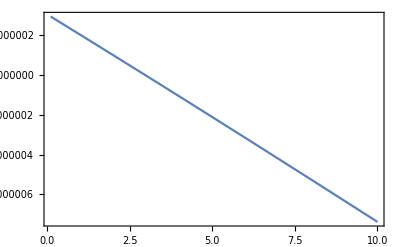
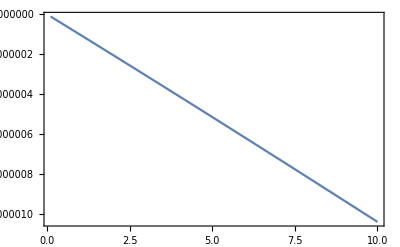
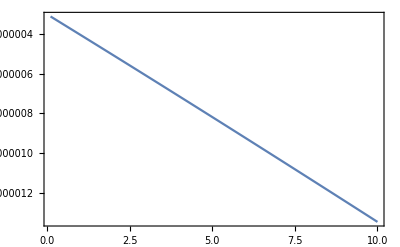
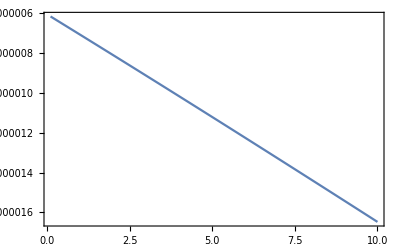

```mathematica
{Plot[EqnSpecX[xx/mee,1/5,-2],{xx,1/10,10},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/5,-1],{xx,1/10,10},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/5,0],{xx,1/10,10},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/5,1],{xx,1/10,10},Frame->True,PlotRange->Full]}(*нет пиков*)
```

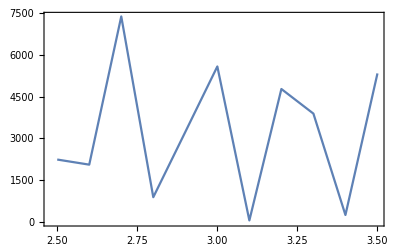
{-Graphics-,-Graphics-}

```mathematica
testp=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,2.5,3.5,0.1}];
testm=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,2.5,3.5,0.1}];
{ListLinePlot[testp,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[testm,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
EqnSpecX[xx/mee,1/5,-2]/.{xx->1/10}
EqnSpecX[xx/mee,1/5,-1]/.{xx->1/10}
EqnSpecX[xx/mee,1/5,0]/.{xx->1/10}
```

2.92964×10^-6

-1.01994×10^-7

-3.13362×10^-6

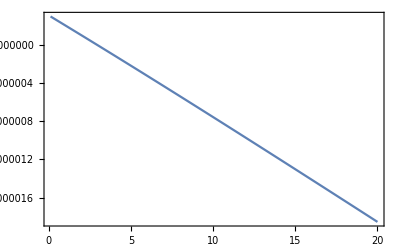
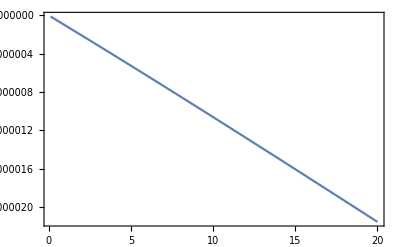
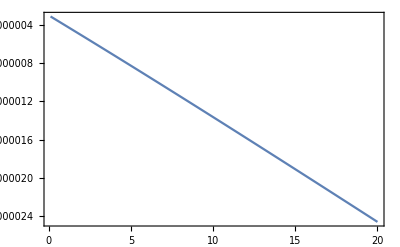
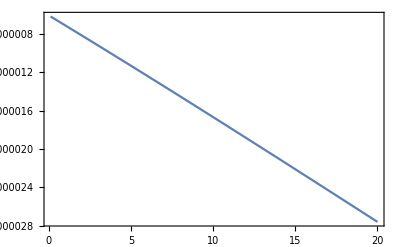

```mathematica
{Plot[EqnSpecX[xx/mee,1/10,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/10,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/10,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/10,1],{xx,1/10,20},Frame->True,PlotRange->Full]}(*нет пиков*)
```

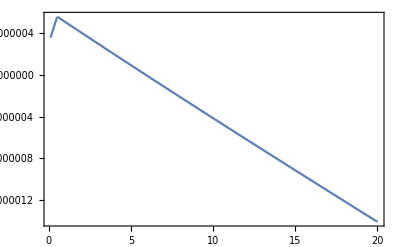
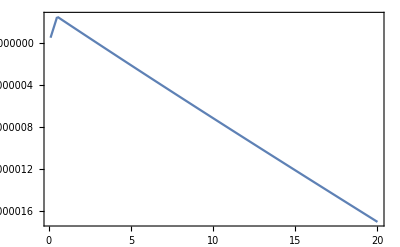
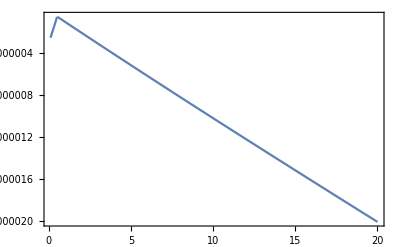
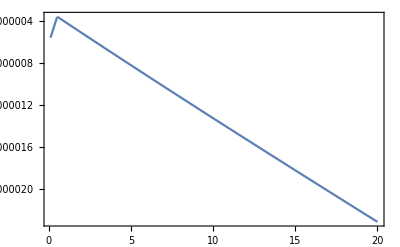

```mathematica
{Plot[EqnSpecY[xx/mee,1/100,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/100,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/100,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/100,1],{xx,1/10,20},Frame->True,PlotRange->Full]}(*нет пиков*)
```

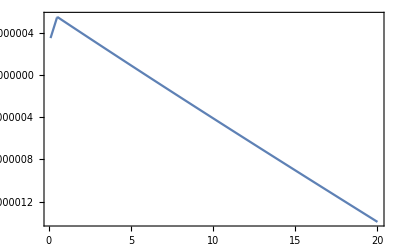
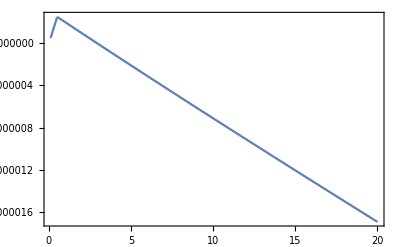
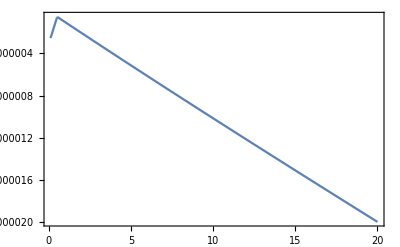
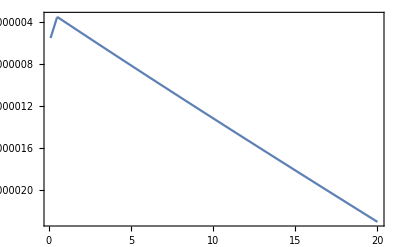

```mathematica
{Plot[EqnSpecY[xx/mee,1/10,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/10,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/10,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/10,1],{xx,1/10,20},Frame->True,PlotRange->Full]}(*нет пиков*)
```

```mathematica
FindRoot[EqnSpecY[xx/mee,1/10,-2],{xx,5}]
FindRoot[EqnSpecY[xx/mee,1/10,-1],{xx,5}]
```

{xx→5.92016}

{xx→2.94055}

```mathematica
FindRoot[EqnSpecX[xx/mee,1/10,-2],{xx,5}]
```

{xx→2.89943}

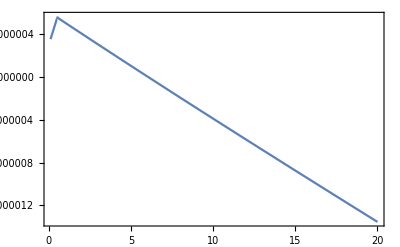
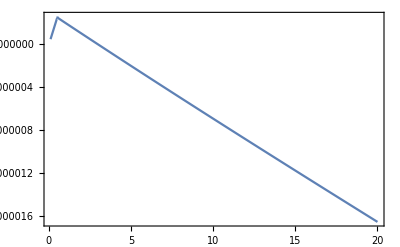
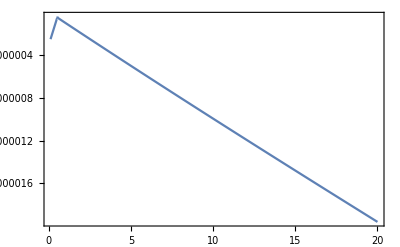
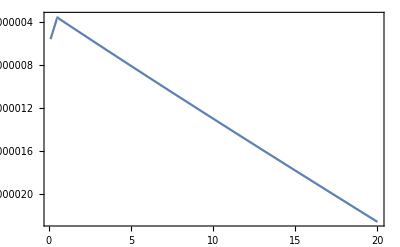

```mathematica
{Plot[EqnSpecY[xx/mee,1/5,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,1],{xx,1/10,20},Frame->True,PlotRange->Full]}(*нет пиков*)
```

```mathematica
FindRoot[EqnSpecY[xx/mee,1/5,-2],{xx,5}]
FindRoot[EqnSpecY[xx/mee,1/5,-1],{xx,5}]
```

{xx→6.03793}

{xx→2.99827}

```mathematica
FindRoot[EqnSpecX[xx/mee,1/5,-2],{xx,5}]
```

{xx→2.95478}

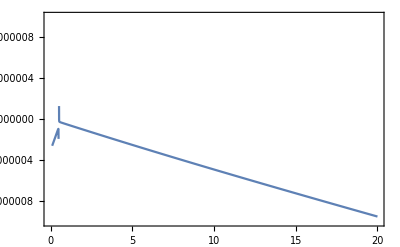

```mathematica
Plot[EqnSpecY[xx/mee,9/10,0],{xx,1/10,20},Frame->True,PlotRange->{-10^(-5),10^(-5)}]
```

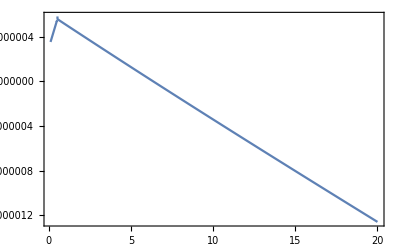
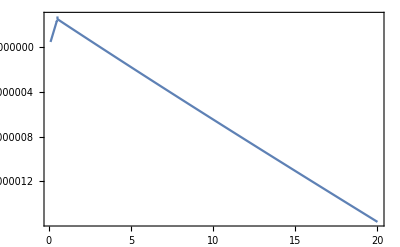
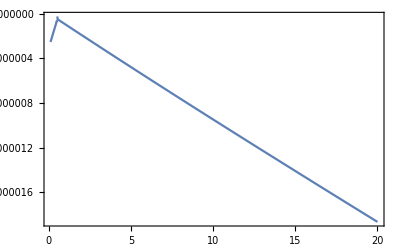
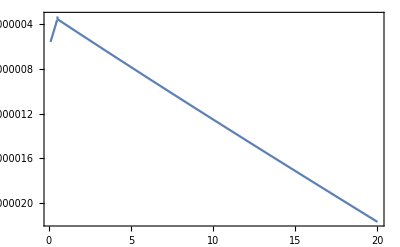

```mathematica
{Plot[EqnSpecY[xx/mee,1/3,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/3,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/3,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/3,1],{xx,1/10,20},Frame->True,PlotRange->Full]}(*слабый пик около 3 мев*)
```

```mathematica
FindRoot[EqnSpecY[xx/mee,1/3,-2],{xx,6}]
FindRoot[EqnSpecY[xx/mee,1/3,-1],{xx,4}]
```

{xx→6.337}

{xx→3.14468}

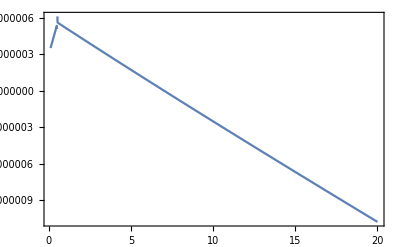
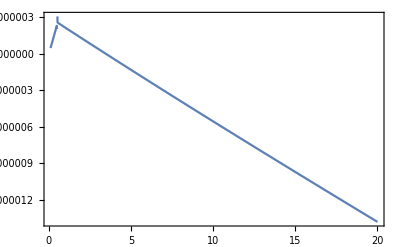
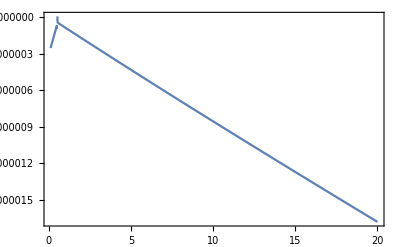
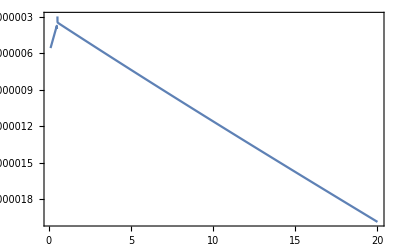

```mathematica
{Plot[EqnSpecY[xx/mee,1/2,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/2,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/2,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/2,1],{xx,1/10,20},Frame->True,PlotRange->Full]}(*есть хороший пик*)
```

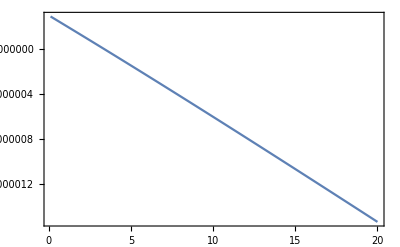
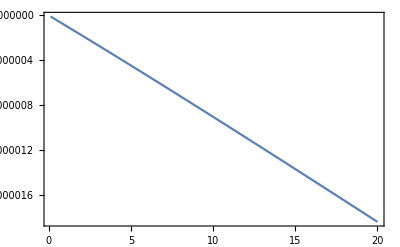
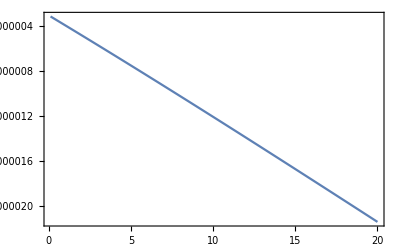
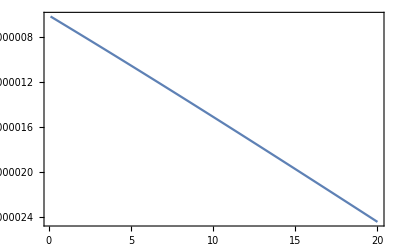

```mathematica
{Plot[EqnSpecX[xx/mee,1/2,-2],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/2,-1],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/2,0],{xx,1/10,20},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/2,1],{xx,1/10,20},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecX[xx/mee,1/2,-2],{xx,4}]
```

{xx→3.40999}

```mathematica
FindRoot[EqnSpecY[xx/mee,1/2,-1],{xx,5}]
```

{xx→3.47662}

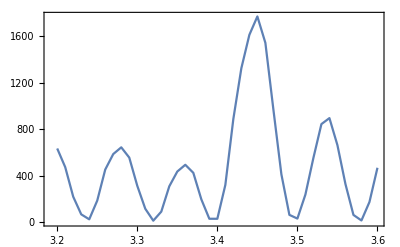
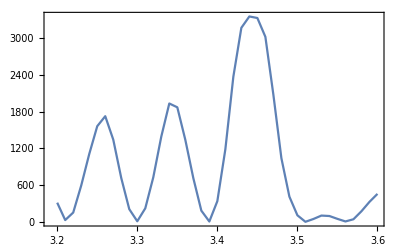

```mathematica
testp=ParallelTable[{x,dProbabPlane[1,x/mee,1/2,0]},{x,3.2,3.6,0.01}];
testm=ParallelTable[{x,dProbabPlane[-1,x/mee,1/2,0]},{x,3.2,3.6,0.01}];
{ListLinePlot[testp,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[testm,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
dProbabPlane[-1,3.477/mee,1/2,0]//Timing
dProbabPlane0[-1,3.477/mee,1/2,0]//Timing
dProbabPlane[1,3.477/mee,1/2,0]//Timing
dProbabPlane0[1,3.477/mee,1/2,0]//Timing
```

{3.57242,1265.19}

{3.55682,1459.1}

{3.88442,545.607}

{3.90003,115.558}

```mathematica
dProbabPlane[-1,3.043/mee,1/4,0]//Timing
dProbabPlane0[-1,3.043/mee,1/4,0]//Timing
dProbabPlane[1,3.043/mee,1/4,0]//Timing
dProbabPlane0[1,3.043/mee,1/4,0]//Timing
```

{3.41642,382.43}

{3.35402,312.107}

{3.88442,3694.65}

{3.86882,6.90039}

```mathematica
γ
βp
```

500.

0.999998

```mathematica
FindRoot[EqnSpecY[xx/mee,1/4,-1],{xx,5}]
```

{xx→3.04309}

```mathematica
dProbabPlane[-1,3.477/mee,1/2,0]//Timing
dProbabPlane0[-1,3.477/mee,1/2,0]//Timing
dProbabPlane[1,3.477/mee,1/2,0]//Timing
dProbabPlane0[1,3.477/mee,1/2,0]//Timing
```

{16.0213,38767.7}

{16.1773,39416.9}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{20.1865,1337.88}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{20.1397,1133.95}

```mathematica
FindRoot[EqnSpecY[xx/mee,1/4,-1],{xx,5}]
```

{xx→3.04313}

```mathematica
dProbabPlane[-1,3.04/mee,1/4,0]//Timing
dProbabPlane0[-1,3.04/mee,1/4,0]//Timing
dProbabPlane[1,3.04/mee,1/4,0]//Timing
dProbabPlane0[1,3.04/mee,1/4,0]//Timing
```

{15.8965,13696.5}

{16.0837,6500.07}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{30.5606,925.784}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{31.0442,0.689147}

```mathematica
tk06s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/2,0]},{x,3,4,0.005}](*нужно еще посмотреть обыкновенную волну*)
```

(3. | 216.829
3.005 | 369.865
3.01 | 479.985
3.015 | 505.486
3.02 | 625.158
3.025 | 638.196
3.03 | 588.944
3.035 | 560.117
3.04 | 487.915
3.045 | 354.867
3.05 | 252.095
3.055 | 182.556
3.06 | 79.085
3.065 | 38.1925
3.07 | 59.9461
3.075 | 101.782
3.08 | 137.578
3.085 | 286.339
3.09 | 396.849
3.095 | 446.975
3.1 | 610.973
3.105 | 637.38
3.11 | 629.906
3.115 | 646.834
3.12 | 571.476
3.125 | 460.249
3.13 | 358.75
3.135 | 262.731
3.14 | 129.978
3.145 | 66.0861
3.15 | 44.4851
3.155 | 41.9084
3.16 | 67.7979
3.165 | 190.805
3.17 | 293.168
3.175 | 361.179
3.18 | 553.147
3.185 | 596.629
3.19 | 634.701
3.195 | 701.012
3.2 | 633.296
3.205 | 563.337
3.21 | 472.356
3.215 | 360.545
3.22 | 217.155
3.225 | 128.844
3.23 | 65.1104
3.235 | 16.3094
3.24 | 22.2512
3.245 | 101.408
3.25 | 183.796
3.255 | 256.591
3.26 | 451.556
3.265 | 509.891
3.27 | 585.13
3.275 | 694.421
3.28 | 643.182
3.285 | 624.332
3.29 | 554.558
3.295 | 441.719
3.3 | 311.442
3.305 | 206.011
3.31 | 113.432
3.315 | 29.1684
3.32 | 10.4953
3.325 | 38.7951
3.33 | 88.6146
3.335 | 147.016
3.34 | 307.082
3.345 | 360.103
3.35 | 434.474
3.355 | 542.663
3.36 | 492.571
3.365 | 483.559
3.37 | 423.272
3.375 | 306.335
3.38 | 194.865
3.385 | 104.817
3.39 | 27.0874
3.395 | 0.982203
3.4 | 26.865
3.405 | 160.797
3.41 | 318.71
3.415 | 490.22
3.42 | 887.982
3.425 | 1025.87
3.43 | 1325.72
3.435 | 1651.82
3.44 | 1613.29
3.445 | 1865.36
3.45 | 1772.08
3.455 | 1612.84
3.46 | 1544.46
3.465 | 1192.79
3.47 | 969.868
3.475 | 666.966
3.48 | 410.415
3.485 | 210.267
3.49 | 60.6279
3.495 | 8.3785
3.5 | 28.6379
3.505 | 112.191
3.51 | 235.86
3.515 | 452.277
3.52 | 552.217
3.525 | 752.872
3.53 | 843.633
3.535 | 847.99
3.54 | 895.204
3.545 | 757.594
3.55 | 661.917
3.555 | 491.259
3.56 | 326.796
3.565 | 186.907
3.57 | 60.1126
3.575 | 11.
3.58 | 12.3289
3.585 | 68.6016
3.59 | 171.698
3.595 | 367.302
3.6 | 466.891
3.605 | 683.01
3.61 | 803.705
3.615 | 839.404
3.62 | 951.621
3.625 | 840.13
3.63 | 784.921
3.635 | 646.729
3.64 | 466.55
3.645 | 327.085
3.65 | 155.458
3.655 | 65.6298
3.66 | 3.67361
3.665 | 12.0948
3.67 | 69.961
3.675 | 219.009
3.68 | 322.249
3.685 | 530.919
3.69 | 684.549
3.695 | 760.519
3.7 | 933.013
3.705 | 870.031
3.71 | 869.192
3.715 | 783.927
3.72 | 606.658
3.725 | 491.292
3.73 | 288.969
3.735 | 165.835
3.74 | 53.2272
3.745 | 3.51621
3.75 | 9.93796
3.755 | 95.612
3.76 | 185.709
3.765 | 362.677
3.77 | 531.513
3.775 | 637.37
3.78 | 849.563
3.785 | 843.467
3.79 | 897.649
3.795 | 876.603
3.8 | 722.049
3.805 | 650.389
3.81 | 438.972
3.815 | 297.159
3.82 | 156.045
3.825 | 46.3606
3.83 | 4.75801
3.835 | 19.7726
3.84 | 79.2509
3.845 | 207.03
3.85 | 368.585
3.855 | 488.135
3.86 | 714.099
3.865 | 763.766
3.87 | 864.642
3.875 | 909.483
3.88 | 794.986
3.885 | 778.292
3.89 | 581.724
3.895 | 439.077
3.9 | 294.414
3.905 | 132.323
3.91 | 53.6743
3.915 | 0.930423
3.92 | 16.3473
3.925 | 86.8905
3.93 | 218.895
3.935 | 334.184
3.94 | 548.199
3.945 | 643.354
3.95 | 776.202
3.955 | 879.2
3.96 | 816.178
3.965 | 855.95
3.97 | 696.026
3.975 | 570.067
3.98 | 444.497
3.985 | 245.891
3.99 | 145.799
3.995 | 37.1183
4. | 1.94665)

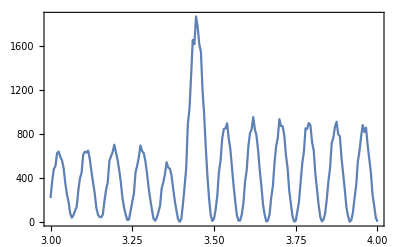

```mathematica
ListLinePlot[tk06s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk06sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/2,0]},{x,3,4,0.005}]
```

(3. | 1578.96
3.005 | 1515.89
3.01 | 1164.39
3.015 | 917.418
3.02 | 619.349
3.025 | 339.397
3.03 | 155.974
3.035 | 44.0329
3.04 | 43.2056
3.045 | 153.154
3.05 | 343.822
3.055 | 580.115
3.06 | 942.914
3.065 | 1126.27
3.07 | 1450.7
3.075 | 1614.26
3.08 | 1600.4
3.085 | 1713.94
3.09 | 1462.9
3.095 | 1287.77
3.1 | 1046.12
3.105 | 698.496
3.11 | 465.
3.115 | 213.34
3.12 | 77.9216
3.125 | 21.9061
3.13 | 85.0539
3.135 | 216.834
3.14 | 493.535
3.145 | 704.496
3.15 | 1039.82
3.155 | 1324.75
3.16 | 1426.86
3.165 | 1702.37
3.17 | 1602.26
3.175 | 1541.82
3.18 | 1438.87
3.185 | 1091.38
3.19 | 885.955
3.195 | 561.455
3.2 | 313.969
3.205 | 129.23
3.21 | 29.9178
3.215 | 29.2056
3.22 | 152.823
3.225 | 321.399
3.23 | 594.917
3.235 | 922.086
3.24 | 1108.21
3.245 | 1495.04
3.25 | 1563.28
3.255 | 1637.3
3.26 | 1726.6
3.265 | 1447.7
3.27 | 1344.37
3.275 | 1034.53
3.28 | 716.41
3.285 | 474.117
3.29 | 208.215
3.295 | 70.3719
3.3 | 10.3009
3.305 | 67.5502
3.31 | 221.7
3.315 | 503.65
3.32 | 728.372
3.325 | 1164.45
3.33 | 1393.78
3.335 | 1613.16
3.34 | 1934.4
3.345 | 1790.57
3.35 | 1871.89
3.355 | 1679.2
3.36 | 1341.44
3.365 | 1145.67
3.37 | 715.609
3.375 | 441.62
3.38 | 184.239
3.385 | 33.5301
3.39 | 6.22221
3.395 | 135.402
3.4 | 338.725
3.405 | 776.02
3.41 | 1184.79
3.415 | 1632.73
3.42 | 2371.71
3.425 | 2551.43
3.43 | 3170.82
3.435 | 3479.42
3.44 | 3356.03
3.445 | 3814.06
3.45 | 3330.85
3.455 | 3150.03
3.46 | 3023.69
3.465 | 2262.93
3.47 | 2076.99
3.475 | 1529.85
3.48 | 1041.34
3.485 | 820.19
3.49 | 412.751
3.495 | 237.759
3.5 | 107.89
3.505 | 16.7659
3.51 | 1.68663
3.515 | 18.2934
3.52 | 47.3954
3.525 | 75.1921
3.53 | 103.233
3.535 | 110.631
3.54 | 96.0277
3.545 | 76.4102
3.55 | 49.5044
3.555 | 16.9293
3.56 | 7.338
3.565 | 7.75064
3.57 | 43.0959
3.575 | 79.3168
3.58 | 174.027
3.585 | 242.711
3.59 | 326.887
3.595 | 436.821
3.6 | 457.593
3.605 | 531.8
3.61 | 513.656
3.615 | 480.337
3.62 | 441.633
3.625 | 331.871
3.63 | 261.683
3.635 | 150.679
3.64 | 79.5424
3.645 | 24.22
3.65 | 2.73324
3.655 | 14.4623
3.66 | 77.6429
3.665 | 152.965
3.67 | 248.203
3.675 | 395.595
3.68 | 453.926
3.685 | 587.497
3.69 | 625.886
3.695 | 628.552
3.7 | 656.281
3.705 | 545.26
3.71 | 492.77
3.715 | 367.628
3.72 | 248.731
3.725 | 157.876
3.73 | 56.7466
3.735 | 16.3224
3.74 | 2.08828
3.745 | 35.2835
3.75 | 94.1611
3.755 | 220.525
3.76 | 301.343
3.765 | 452.462
3.77 | 554.977
3.775 | 607.564
3.78 | 716.324
3.785 | 658.485
3.79 | 658.4
3.795 | 579.932
3.8 | 450.991
3.805 | 370.399
3.81 | 214.816
3.815 | 128.606
3.82 | 44.7192
3.825 | 4.30295
3.83 | 4.81026
3.835 | 61.1667
3.84 | 127.459
3.845 | 248.269
3.85 | 378.974
3.855 | 465.058
3.86 | 628.009
3.865 | 645.125
3.87 | 705.687
3.875 | 711.414
3.88 | 613.325
3.885 | 584.303
3.89 | 424.061
3.895 | 318.386
3.9 | 204.606
3.905 | 88.1779
3.91 | 34.0021
3.915 | 0.0815504
3.92 | 16.6264
3.925 | 73.7816
3.93 | 180.559
3.935 | 268.638
3.94 | 437.465
3.945 | 518.445
3.95 | 624.256
3.955 | 718.12
3.96 | 680.115
3.965 | 723.712
3.97 | 611.76
3.975 | 520.512
3.98 | 428.314
3.985 | 262.562
3.99 | 177.591
3.995 | 67.5311
4. | 15.4269)

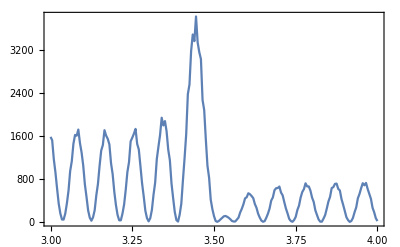

```mathematica
ListLinePlot[tk06sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk08s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/2,0]},{x,3.3,3.6,0.001}]
```

(3.3 | 311.442
3.301 | 286.03
3.302 | 262.908
3.303 | 242.192
3.304 | 223.466
3.305 | 206.011
3.306 | 189.011
3.307 | 171.698
3.308 | 153.464
3.309 | 133.995
3.31 | 113.432
3.311 | 92.4959
3.312 | 72.4246
3.313 | 54.6153
3.314 | 40.0955
3.315 | 29.1684
3.316 | 21.4631
3.317 | 16.2769
3.318 | 12.9402
3.319 | 11.0399
3.32 | 10.4953
3.321 | 11.5336
3.322 | 14.5896
3.323 | 20.1168
3.324 | 28.306
3.325 | 38.7951
3.326 | 50.5743
3.327 | 62.2691
3.328 | 72.7033
3.329 | 81.3802
3.33 | 88.6146
3.331 | 95.3706
3.332 | 103.017
3.333 | 113.131
3.334 | 127.326
3.335 | 147.016
3.336 | 172.996
3.337 | 204.846
3.338 | 240.415
3.339 | 275.928
3.34 | 307.082
3.341 | 330.706
3.342 | 345.905
3.343 | 354.014
3.344 | 357.714
3.345 | 360.103
3.346 | 364.107
3.347 | 372.212
3.348 | 386.278
3.349 | 407.214
3.35 | 434.474
3.351 | 465.574
3.352 | 496.201
3.353 | 521.361
3.354 | 537.251
3.355 | 542.663
3.356 | 538.992
3.357 | 529.16
3.358 | 516.402
3.359 | 503.511
3.36 | 492.571
3.361 | 484.912
3.362 | 481.074
3.363 | 480.679
3.364 | 482.298
3.365 | 483.559
3.366 | 481.758
3.367 | 474.838
3.368 | 462.147
3.369 | 444.446
3.37 | 423.272
3.371 | 400.214
3.372 | 376.475
3.373 | 352.768
3.374 | 329.385
3.375 | 306.335
3.376 | 283.498
3.377 | 260.777
3.378 | 238.232
3.379 | 216.13
3.38 | 194.865
3.381 | 174.766
3.382 | 155.936
3.383 | 138.216
3.384 | 121.291
3.385 | 104.817
3.386 | 88.5315
3.387 | 72.3332
3.388 | 56.3559
3.389 | 41.0282
3.39 | 27.0874
3.391 | 15.4671
3.392 | 7.00479
3.393 | 2.06165
3.394 | 0.322769
3.395 | 0.982203
3.396 | 3.19925
3.397 | 6.51274
3.398 | 11.031
3.399 | 17.431
3.4 | 26.865
3.401 | 40.8042
3.402 | 60.7603
3.403 | 87.7873
3.404 | 121.769
3.405 | 160.797
3.406 | 201.246
3.407 | 238.968
3.408 | 271.061
3.409 | 297.028
3.41 | 318.71
3.411 | 339.435
3.412 | 363.153
3.413 | 393.875
3.414 | 435.286
3.415 | 490.22
3.416 | 559.727
3.417 | 641.772
3.418 | 730.248
3.419 | 815.623
3.42 | 887.982
3.421 | 941.165
3.422 | 975.149
3.423 | 995.237
3.424 | 1009.4
3.425 | 1025.87
3.426 | 1051.8
3.427 | 1092.78
3.428 | 1152.39
3.429 | 1231.26
3.43 | 1325.72
3.431 | 1426.75
3.432 | 1520.81
3.433 | 1593.95
3.434 | 1637.56
3.435 | 1651.82
3.436 | 1644.61
3.437 | 1627.31
3.438 | 1610.97
3.439 | 1604.33
3.44 | 1613.29
3.441 | 1640.83
3.442 | 1686.63
3.443 | 1746.19
3.444 | 1810.16
3.445 | 1865.36
3.446 | 1898.48
3.447 | 1901.55
3.448 | 1875.36
3.449 | 1828.35
3.45 | 1772.08
3.451 | 1717.14
3.452 | 1671.05
3.453 | 1637.99
3.454 | 1619.13
3.455 | 1612.84
3.456 | 1614.65
3.457 | 1617.17
3.458 | 1611.21
3.459 | 1588.33
3.46 | 1544.46
3.461 | 1481.84
3.462 | 1407.69
3.463 | 1330.64
3.464 | 1257.67
3.465 | 1192.79
3.466 | 1137.26
3.467 | 1090.18
3.468 | 1049.13
3.469 | 1010.47
3.47 | 969.868
3.471 | 923.14
3.472 | 867.72
3.473 | 803.993
3.474 | 735.421
3.475 | 666.966
3.476 | 602.924
3.477 | 545.607
3.478 | 495.291
3.479 | 450.843
3.48 | 410.415
3.481 | 371.944
3.482 | 333.527
3.483 | 293.799
3.484 | 252.385
3.485 | 210.267
3.486 | 169.679
3.487 | 133.267
3.488 | 102.905
3.489 | 78.9906
3.49 | 60.6279
3.491 | 46.321
3.492 | 34.6322
3.493 | 24.566
3.494 | 15.7295
3.495 | 8.3785
3.496 | 3.38404
3.497 | 2.04506
3.498 | 5.63565
3.499 | 14.7242
3.5 | 28.6379
3.501 | 45.5776
3.502 | 63.4214
3.503 | 80.6338
3.504 | 96.7202
3.505 | 112.191
3.506 | 128.313
3.507 | 146.849
3.508 | 169.814
3.509 | 199.101
3.51 | 235.86
3.511 | 279.632
3.512 | 327.7
3.513 | 375.435
3.514 | 417.972
3.515 | 452.277
3.516 | 478.149
3.517 | 497.726
3.518 | 514.316
3.519 | 531.424
3.52 | 552.217
3.521 | 579.234
3.522 | 614.027
3.523 | 656.565
3.524 | 704.497
3.525 | 752.872
3.526 | 795.181
3.527 | 825.806
3.528 | 842.496
3.529 | 846.992
3.53 | 843.633
3.531 | 837.362
3.532 | 832.379
3.533 | 831.635
3.534 | 836.758
3.535 | 847.99
3.536 | 863.972
3.537 | 881.502
3.538 | 895.751
3.539 | 901.492
3.54 | 895.204
3.541 | 876.779
3.542 | 849.402
3.543 | 817.784
3.544 | 786.226
3.545 | 757.594
3.546 | 733.179
3.547 | 712.948
3.548 | 695.793
3.549 | 679.692
3.55 | 661.917
3.551 | 639.553
3.552 | 610.478
3.553 | 574.473
3.554 | 533.589
3.555 | 491.259
3.556 | 450.742
3.557 | 414.022
3.558 | 381.618
3.559 | 352.948
3.56 | 326.796
3.561 | 301.661
3.562 | 276.016
3.563 | 248.585
3.564 | 218.736
3.565 | 186.907
3.566 | 154.733
3.567 | 124.531
3.568 | 98.3009
3.569 | 76.9277
3.57 | 60.1126
3.571 | 46.8549
3.572 | 36.0143
3.573 | 26.6809
3.574 | 18.3515
3.575 | 11.
3.576 | 5.08942
3.577 | 1.48815
3.578 | 1.1973
3.579 | 4.86768
3.58 | 12.3289
3.581 | 22.5314
3.582 | 34.0396
3.583 | 45.7135
3.584 | 57.1236
3.585 | 68.6016
3.586 | 81.1021
3.587 | 96.0359
3.588 | 115.09
3.589 | 139.938
3.59 | 171.698
3.591 | 210.145
3.592 | 253.028
3.593 | 296.251
3.594 | 335.32
3.595 | 367.302
3.596 | 391.876
3.597 | 410.957
3.598 | 427.631
3.599 | 445.241
3.6 | 466.891)

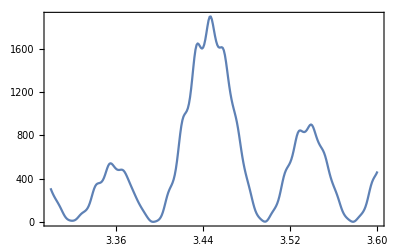

```mathematica
ListLinePlot[tk08s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk08sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/2,0]},{x,3.3,3.6,0.001}]
```

(3.3 | 10.3009
3.301 | 15.5386
3.302 | 25.0877
3.303 | 37.3961
3.304 | 51.5568
3.305 | 67.5502
3.306 | 86.2124
3.307 | 109.08
3.308 | 138.128
3.309 | 175.299
3.31 | 221.7
3.311 | 276.604
3.312 | 336.862
3.313 | 397.557
3.314 | 453.976
3.315 | 503.65
3.316 | 547.098
3.317 | 587.169
3.318 | 627.907
3.319 | 673.635
3.32 | 728.372
3.321 | 795.278
3.322 | 875.819
3.323 | 968.528
3.324 | 1067.87
3.325 | 1164.45
3.326 | 1247.68
3.327 | 1310.25
3.328 | 1351.33
3.329 | 1376.3
3.33 | 1393.78
3.331 | 1412.63
3.332 | 1440.14
3.333 | 1481.46
3.334 | 1539.26
3.335 | 1613.16
3.336 | 1698.65
3.337 | 1786.33
3.338 | 1862.84
3.339 | 1914.77
3.34 | 1934.4
3.341 | 1923.4
3.342 | 1891.49
3.343 | 1851.58
3.344 | 1815.25
3.345 | 1790.57
3.346 | 1781.84
3.347 | 1789.94
3.348 | 1812.39
3.349 | 1843.03
3.35 | 1871.89
3.351 | 1886.49
3.352 | 1875.46
3.353 | 1833.56
3.354 | 1764.52
3.355 | 1679.2
3.356 | 1590.37
3.357 | 1508.23
3.358 | 1438.66
3.359 | 1383.49
3.36 | 1341.44
3.361 | 1308.87
3.362 | 1280.14
3.363 | 1248.07
3.364 | 1205.1
3.365 | 1145.67
3.366 | 1068.89
3.367 | 979.513
3.368 | 885.884
3.369 | 796.162
3.37 | 715.609
3.371 | 646.008
3.372 | 586.493
3.373 | 534.669
3.374 | 487.449
3.375 | 441.62
3.376 | 394.359
3.377 | 343.91
3.378 | 290.344
3.379 | 235.893
3.38 | 184.239
3.381 | 138.889
3.382 | 101.729
3.383 | 72.7113
3.384 | 50.5281
3.385 | 33.5301
3.386 | 20.3978
3.387 | 10.4993
3.388 | 4.04115
3.389 | 2.06652
3.39 | 6.22221
3.391 | 18.1555
3.392 | 38.5933
3.393 | 66.6108
3.394 | 99.7988
3.395 | 135.402
3.396 | 171.613
3.397 | 208.211
3.398 | 246.503
3.399 | 288.943
3.4 | 338.725
3.401 | 399.323
3.402 | 473.757
3.403 | 563.357
3.404 | 666.184
3.405 | 776.02
3.406 | 883.47
3.407 | 979.59
3.408 | 1059.96
3.409 | 1126.25
3.41 | 1184.79
3.411 | 1243.9
3.412 | 1311.91
3.413 | 1396.14
3.414 | 1502.16
3.415 | 1632.73
3.416 | 1786.01
3.417 | 1953.42
3.418 | 2119.17
3.419 | 2263.75
3.42 | 2371.71
3.421 | 2438.96
3.422 | 2474.07
3.423 | 2493.32
3.424 | 2514.22
3.425 | 2551.43
3.426 | 2615.39
3.427 | 2712.05
3.428 | 2842.25
3.429 | 3000.06
3.43 | 3170.82
3.431 | 3331.09
3.432 | 3453.76
3.433 | 3518.58
3.434 | 3522.17
3.435 | 3479.42
3.436 | 3415.54
3.437 | 3355.8
3.438 | 3319.38
3.439 | 3317.88
3.44 | 3356.03
3.441 | 3432.07
3.442 | 3537.01
3.443 | 3653.33
3.444 | 3755.3
3.445 | 3814.06
3.446 | 3808.36
3.447 | 3735.28
3.448 | 3612.22
3.449 | 3468.02
3.45 | 3330.85
3.451 | 3220.75
3.452 | 3148.27
3.453 | 3115.94
3.454 | 3119.84
3.455 | 3150.03
3.456 | 3190.1
3.457 | 3217.67
3.458 | 3208.43
3.459 | 3144.54
3.46 | 3023.69
3.461 | 2861.36
3.462 | 2683.32
3.463 | 2514.51
3.464 | 2371.82
3.465 | 2262.93
3.466 | 2188.17
3.467 | 2142.74
3.468 | 2117.89
3.469 | 2101.15
3.47 | 2076.99
3.471 | 2029.27
3.472 | 1946.39
3.473 | 1827.1
3.474 | 1682.24
3.475 | 1529.85
3.476 | 1387.13
3.477 | 1265.19
3.478 | 1168.16
3.479 | 1094.96
3.48 | 1041.34
3.481 | 1001.14
3.482 | 966.86
3.483 | 930.172
3.484 | 883.069
3.485 | 820.19
3.486 | 741.421
3.487 | 652.623
3.488 | 563.106
3.489 | 481.463
3.49 | 412.751
3.491 | 358.191
3.492 | 316.356
3.493 | 284.49
3.494 | 259.376
3.495 | 237.759
3.496 | 216.605
3.497 | 193.464
3.498 | 167.053
3.499 | 137.82
3.5 | 107.89
3.501 | 80.1131
3.502 | 56.7428
3.503 | 38.7017
3.504 | 25.6959
3.505 | 16.7659
3.506 | 10.7982
3.507 | 6.82789
3.508 | 4.17069
3.509 | 2.46806
3.51 | 1.68663
3.511 | 2.05507
3.512 | 3.89761
3.513 | 7.38495
3.514 | 12.346
3.515 | 18.2934
3.516 | 24.635
3.517 | 30.8907
3.518 | 36.7901
3.519 | 42.2642
3.52 | 47.3954
3.521 | 52.3686
3.522 | 57.4296
3.523 | 62.8319
3.524 | 68.7539
3.525 | 75.1921
3.526 | 81.894
3.527 | 88.4159
3.528 | 94.3041
3.529 | 99.2687
3.53 | 103.233
3.531 | 106.264
3.532 | 108.475
3.533 | 109.947
3.534 | 110.689
3.535 | 110.631
3.536 | 109.646
3.537 | 107.61
3.538 | 104.504
3.539 | 100.513
3.54 | 96.0277
3.541 | 91.5069
3.542 | 87.2855
3.543 | 83.4627
3.544 | 79.9212
3.545 | 76.4102
3.546 | 72.6228
3.547 | 68.2481
3.548 | 63.0151
3.549 | 56.7559
3.55 | 49.5044
3.551 | 41.5999
3.552 | 33.7043
3.553 | 26.6248
3.554 | 20.9784
3.555 | 16.9293
3.556 | 14.1969
3.557 | 12.2773
3.558 | 10.6813
3.559 | 9.0757
3.56 | 7.338
3.561 | 5.57535
3.562 | 4.13388
3.563 | 3.5808
3.564 | 4.60029
3.565 | 7.75064
3.566 | 13.1425
3.567 | 20.2678
3.568 | 28.188
3.569 | 35.978
3.57 | 43.0959
3.571 | 49.4935
3.572 | 55.5421
3.573 | 61.9164
3.574 | 69.5046
3.575 | 79.3168
3.576 | 92.3143
3.577 | 109.08
3.578 | 129.362
3.579 | 151.768
3.58 | 174.027
3.581 | 193.905
3.582 | 210.167
3.583 | 222.912
3.584 | 233.24
3.585 | 242.711
3.586 | 252.966
3.587 | 265.521
3.588 | 281.643
3.589 | 302.12
3.59 | 326.887
3.591 | 354.573
3.592 | 382.394
3.593 | 406.871
3.594 | 425.271
3.595 | 436.821
3.596 | 442.775
3.597 | 445.524
3.598 | 447.605
3.599 | 451.128
3.6 | 457.593)

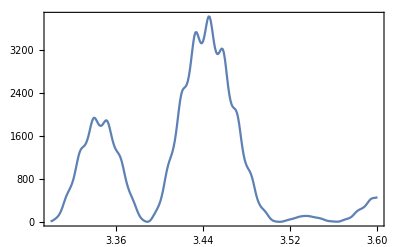

```mathematica
ListLinePlot[tk08sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk07s1=ParallelTable[{x,dProbabPlane[1,x/mee,1/4,0]},{x,2.5,3.5,0.005}]
```

(2.5 | 3274.95
2.505 | 3898.71
2.51 | 4620.45
2.515 | 4374.06
2.52 | 4388.41
2.525 | 3440.2
2.53 | 2721.55
2.535 | 1751.12
2.54 | 818.065
2.545 | 318.39
2.55 | 0.317075
2.555 | 114.78
2.56 | 679.048
2.565 | 1442.13
2.57 | 2267.27
2.575 | 3394.61
2.58 | 3816.27
2.585 | 4560.84
2.59 | 4306.66
2.595 | 4133.57
2.6 | 3420.5
2.605 | 2457.86
2.61 | 1716.59
2.615 | 699.59
2.62 | 260.494
2.625 | 0.926494
2.63 | 173.038
2.635 | 657.421
2.64 | 1579.
2.645 | 2259.07
2.65 | 3425.56
2.655 | 3836.1
2.66 | 4377.82
2.665 | 4329.44
2.67 | 3862.37
2.675 | 3400.57
2.68 | 2258.04
2.685 | 1593.48
2.69 | 644.506
2.695 | 187.539
2.7 | 0.684562
2.705 | 239.02
2.71 | 671.699
2.715 | 1660.24
2.72 | 2338.66
2.725 | 3340.17
2.73 | 3930.01
2.735 | 4168.81
2.74 | 4359.89
2.745 | 3658.07
2.75 | 3271.39
2.755 | 2151.55
2.76 | 1405.42
2.765 | 632.848
2.77 | 122.823
2.775 | 0.457692
2.78 | 290.925
2.785 | 743.686
2.79 | 1655.34
2.795 | 2476.31
2.8 | 3218.41
2.805 | 4029.36
2.81 | 4024.81
2.815 | 4281.98
2.82 | 3553.16
2.825 | 3032.98
2.83 | 2121.77
2.835 | 1213.28
2.84 | 609.383
2.845 | 79.1481
2.85 | 8.03646
2.855 | 310.367
2.86 | 855.536
2.865 | 1608.77
2.87 | 2616.74
2.875 | 3151.69
2.88 | 4030.86
2.885 | 3971.09
2.89 | 4064.01
2.895 | 3528.38
2.9 | 2765.47
2.905 | 2085.02
2.91 | 1059.61
2.915 | 536.908
2.92 | 59.2558
2.925 | 27.0661
2.93 | 305.179
2.935 | 969.481
2.94 | 1590.34
2.945 | 2668.02
2.95 | 3140.81
2.955 | 3849.17
2.96 | 3936.49
2.965 | 3733.35
2.97 | 3426.33
2.975 | 2466.12
2.98 | 1875.19
2.985 | 900.539
2.99 | 383.463
2.995 | 34.6676
3. | 77.5296
3.005 | 379.599
3.01 | 1178.94
3.015 | 1804.88
3.02 | 2848.43
3.025 | 3455.41
3.03 | 3916.21
3.035 | 4249.55
3.04 | 3764.41
3.045 | 3564.54
3.05 | 2521.84
3.055 | 1836.31
3.06 | 976.808
3.065 | 341.968
3.07 | 49.8121
3.075 | 83.9336
3.08 | 381.434
3.085 | 1129.45
3.09 | 1846.49
3.095 | 2662.04
3.1 | 3489.49
3.105 | 3698.81
3.11 | 4151.21
3.115 | 3604.34
3.12 | 3298.74
3.125 | 2453.47
3.13 | 1603.25
3.135 | 940.112
3.14 | 259.126
3.145 | 35.9446
3.15 | 100.766
3.155 | 463.854
3.16 | 1110.11
3.165 | 1982.52
3.17 | 2601.01
3.175 | 3538.5
3.18 | 3642.81
3.185 | 3975.38
3.19 | 3575.44
3.195 | 3024.69
3.2 | 2419.98
3.205 | 1417.36
3.21 | 855.24
3.215 | 210.948
3.22 | 20.5221
3.225 | 106.457
3.23 | 561.661
3.235 | 1113.91
3.24 | 2088.46
3.245 | 2625.57
3.25 | 3474.44
3.255 | 3676.65
3.26 | 3740.69
3.265 | 3582.64
3.27 | 2793.27
3.275 | 2311.25
3.28 | 1296.8
3.285 | 722.533
3.29 | 191.049
3.295 | 10.9677
3.3 | 117.688
3.305 | 647.872
3.31 | 1174.97
3.315 | 2112.91
3.32 | 2719.82
3.325 | 3335.72
3.33 | 3746.53
3.335 | 3538.68
3.34 | 3515.59
3.345 | 2640.08
3.35 | 2104.7
3.355 | 1238.4
3.36 | 579.425
3.365 | 174.021
3.37 | 9.58439
3.375 | 152.244
3.38 | 697.005
3.385 | 1286.83
3.39 | 2073.19
3.395 | 2844.85
3.4 | 3218.29
3.405 | 3761.78
3.41 | 3415.73
3.415 | 3319.96
3.42 | 2567.01
3.425 | 1860.41
3.43 | 1194.65
3.435 | 457.538
3.44 | 139.104
3.445 | 13.5902
3.45 | 212.342
3.455 | 710.131
3.46 | 1423.
3.465 | 2045.39
3.47 | 2937.14
3.475 | 3173.93
3.48 | 3652.24
3.485 | 3374.75
3.49 | 3055.85
3.495 | 2526.51
3.5 | 1640.24)

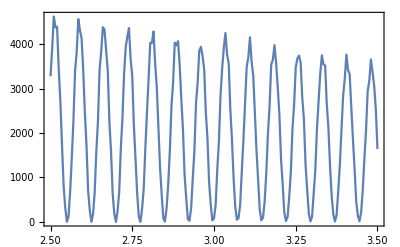

```mathematica
ListLinePlot[tk07s1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
tk07sm1=ParallelTable[{x,dProbabPlane[-1,x/mee,1/4,0]},{x,2.5,3.5,0.005}]
```

(2.5 | 437.064
2.505 | 92.0254
2.51 | 68.0974
2.515 | 457.88
2.52 | 1199.14
2.525 | 2264.58
2.53 | 3068.61
2.535 | 4335.92
2.54 | 4574.67
2.545 | 5151.09
2.55 | 4852.02
2.555 | 4230.71
2.56 | 3644.21
2.565 | 2330.86
2.57 | 1586.27
2.575 | 602.313
2.58 | 154.939
2.585 | 9.11366
2.59 | 335.672
2.595 | 873.433
2.6 | 1973.08
2.605 | 2707.47
2.61 | 3881.84
2.615 | 4437.39
2.62 | 4748.96
2.625 | 4979.49
2.63 | 4174.09
2.635 | 3807.63
2.64 | 2567.13
2.645 | 1724.5
2.65 | 847.166
2.655 | 221.013
2.66 | 9.56967
2.665 | 212.035
2.67 | 652.593
2.675 | 1592.91
2.68 | 2453.93
2.685 | 3351.17
2.69 | 4317.65
2.695 | 4430.61
2.7 | 4931.95
2.705 | 4250.02
2.71 | 3806.05
2.715 | 2903.16
2.72 | 1844.53
2.725 | 1117.06
2.73 | 316.821
2.735 | 48.5654
2.74 | 93.5496
2.745 | 500.491
2.75 | 1194.11
2.755 | 2226.85
2.76 | 2912.24
2.765 | 4069.71
2.77 | 4262.17
2.775 | 4682.19
2.78 | 4439.78
2.785 | 3771.93
2.79 | 3236.64
2.795 | 2023.39
2.8 | 1337.49
2.805 | 482.493
2.81 | 99.7564
2.815 | 16.676
2.82 | 370.618
2.825 | 881.753
2.83 | 1941.42
2.835 | 2620.7
2.84 | 3659.68
2.845 | 4218.74
2.85 | 4404.11
2.855 | 4638.1
2.86 | 3839.44
2.865 | 3456.08
2.87 | 2327.6
2.875 | 1512.86
2.88 | 736.894
2.885 | 164.176
2.89 | 2.65309
2.895 | 237.083
2.9 | 680.207
2.905 | 1584.42
2.91 | 2453.43
2.915 | 3258.37
2.92 | 4242.56
2.925 | 4303.74
2.93 | 4768.45
2.935 | 4139.3
2.94 | 3644.95
2.945 | 2823.95
2.95 | 1749.29
2.955 | 1061.8
2.96 | 282.82
2.965 | 32.8802
2.97 | 111.528
2.975 | 567.978
2.98 | 1305.76
2.985 | 2478.75
2.99 | 3241.52
2.995 | 4621.27
3. | 4960.46
3.005 | 5559.65
3.01 | 5597.27
3.015 | 4903.73
3.02 | 4646.75
3.025 | 3233.18
3.03 | 2504.
3.035 | 1426.21
3.04 | 629.05
3.045 | 206.55
3.05 | 2.56704
3.055 | 123.027
3.06 | 574.445
3.065 | 1084.11
3.07 | 1666.71
3.075 | 2221.49
3.08 | 2458.82
3.085 | 2693.03
3.09 | 2358.22
3.095 | 2159.64
3.1 | 1487.36
3.105 | 989.131
3.11 | 491.966
3.115 | 101.324
3.12 | 1.65964
3.125 | 171.363
3.13 | 488.402
3.135 | 1093.93
3.14 | 1778.39
3.145 | 2296.06
3.15 | 3029.71
3.155 | 3099.99
3.16 | 3376.74
3.165 | 2980.92
3.17 | 2601.77
3.175 | 2019.09
3.18 | 1243.39
3.185 | 764.991
3.19 | 195.844
3.195 | 24.0143
3.2 | 71.998
3.205 | 401.876
3.21 | 856.376
3.215 | 1676.36
3.22 | 2143.35
3.225 | 2937.27
3.23 | 3167.16
3.235 | 3357.82
3.24 | 3270.99
3.245 | 2730.72
3.25 | 2357.16
3.255 | 1463.39
3.26 | 961.27
3.265 | 355.731
3.27 | 60.9719
3.275 | 9.39159
3.28 | 288.908
3.285 | 646.418
3.29 | 1417.54
3.295 | 1977.57
3.3 | 2632.35
3.305 | 3167.66
3.31 | 3230.3
3.315 | 3424.69
3.32 | 2854.61
3.325 | 2536.92
3.33 | 1748.23
3.335 | 1109.09
3.34 | 576.291
3.345 | 115.817
3.35 | 3.08436
3.355 | 162.545
3.36 | 498.3
3.365 | 1087.75
3.37 | 1814.62
3.375 | 2312.9
3.38 | 3068.58
3.385 | 3135.18
3.39 | 3396.41
3.395 | 3032.
3.4 | 2611.27
3.405 | 2075.26
3.41 | 1260.29
3.415 | 793.816
3.42 | 215.097
3.425 | 28.4703
3.43 | 54.847
3.435 | 378.018
3.44 | 797.32
3.445 | 1601.84
3.45 | 2066.79
3.455 | 2818.24
3.46 | 3092.86
3.465 | 3249.72
3.47 | 3224.56
3.475 | 2673.73
3.48 | 2338.2
3.485 | 1467.75
3.49 | 962.304
3.495 | 385.136
3.5 | 67.3862)

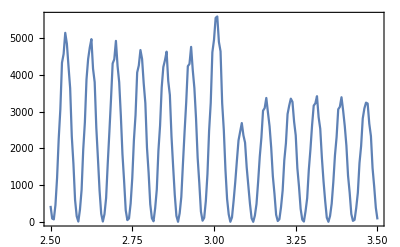

```mathematica
ListLinePlot[tk07sm1,Frame->True,Axes->False,PlotRange->Full]
```

```mathematica
ll2ts1=AmplTwistTab[1,3.45/mee,3.45/mee/2];
ll2tsm1=AmplTwistTab[-1,3.45/mee,3.45/mee/2];
```

```mathematica
tm2s1=Table[{m,dProbabTwist[m,ll2ts1[[3]]]},{m,-mMax,mMax}];
tm2sm1=Table[{m,dProbabTwist[m,ll2tsm1[[3]]]},{m,-mMax,mMax}];
```

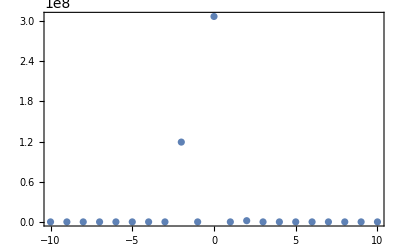
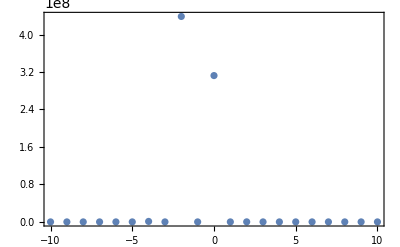

```mathematica
{ListPlot[tm2s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm2sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
ll3ts1=AmplTwistTab[1,3.47/mee,3.47/mee/2];(*смещение на 0.02 эВ оказывается существенным для распределения по m*)
ll3tsm1=AmplTwistTab[-1,3.47/mee,3.47/mee/2];
```

```mathematica
tm3s1=Table[{m,dProbabTwist[m,ll3ts1[[3]]]},{m,-mMax,mMax}];
tm3sm1=Table[{m,dProbabTwist[m,ll3tsm1[[3]]]},{m,-mMax,mMax}];
```

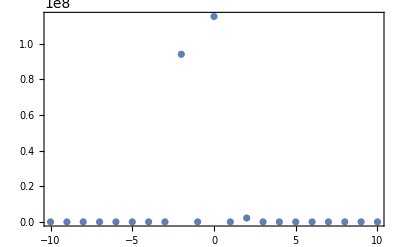
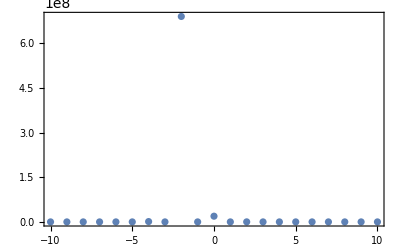

```mathematica
{ListPlot[tm3s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm3sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
llts1=AmplTwistTab[1,3.47/mee,3.47/mee/2];
lltsm1=AmplTwistTab[-1,3.47/mee,3.47/mee/2];
```

```mathematica
tms1=Table[{m,dProbabTwist[m,llts1[[3]]]},{m,-mMax,mMax}];
tmsm1=Table[{m,dProbabTwist[m,lltsm1[[3]]]},{m,-mMax,mMax}];
```

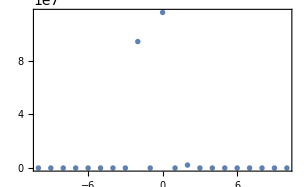
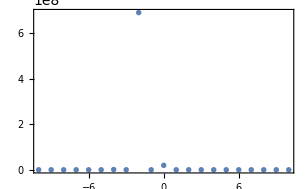

```mathematica
{ListPlot[tms1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tmsm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*------гауссов пучок. нормальное падение-------*)
```

```mathematica
(*===================Задаем параметры амплитуды=====================*)
ss1=1;(*спиральность фотона*)
kom2=3.47/mee;(*энергия излучения*)
np11=SetPrecision[1/2,90];(*n_perp*)
(*NN1=20;(*диапазон ненулевых m*)*)
(*NNl=-15;
NNr=15;*)
sigpc=1/(kom2 np11);
Print["Критическое значение поперечного размера пучка: ",sigpc lc 10^4," мкм"]
"Критическое значение поперечного размера пучка: "0.11368645533141207" мкм"
```

Критическое значение поперечного размера пучка: 0.113686 мкм

Критическое значение поперечного размера пучка: 0.113686 мкм

```mathematica
Np=10^9/(10^4);(*число частиц в пучке*)
sig3=SetPrecision[0.015/lc,90];(*продольный размер. 0.5 ps*)
sigp=SetPrecision[1 10^(-4)/lc,90];(*поперечный размер. 1.25 мкм*)
β3=Sqrt[1-1/γ^2];(*скорость вдоль оси*)
ex=SetPrecision[0.9,90];(*эксцентриситет*)
hx=SetPrecision[0.1,90];(*смещение центра в долях sigp*)
hy=SetPrecision[0.05,90];(*смещение центра в долях sigp*)
ϵy=Sqrt[1-ex^2/2];
ϵx=Sqrt[(1-ex^2/2)/(1-ex^2)];
Print["Продольный размер пучка: ",sig3 lc 10^4," мкм"]
Print["Параметр продольной когерентности: ",kom2 sig3 Sqrt[1-np11^2]]
Print["Параметр размазанности по m: ",kom2 sigp np11]
```

Продольный размер пучка: 150. мкм

Параметр продольной когерентности: 2285.3

Параметр размазанности по m: 8.79612

```mathematica
(*===============Cчитаем амплитуду для разных n_perp и фиксированном kom======================*)
```

```mathematica
npmin=SetPrecision[np11/4,90];(*диапазон npp*)
npmax=SetPrecision[1.5 np11,90];(*диапазон npp*)
npst=10;(*число шагов*)
```

```mathematica
AmplBunchMNpp=Module[{npp2},
Table[{npp2,AmplTwistTab[ss1,kom2,kom2 npp2][[3]]},{npp2,npmin,npmax,(npmax-npmin)/npst}]];
```

```mathematica
Nnpnt=Length[AmplBunchMNpp[[1,2]]];(*число достоверных m*)
AmplBunchMNppf=Module[{mm,nnp,Nn},Nn=Nnpnt;Table[{{mm,nnp},I^(-mm) AmplBunchMNpp[[1+Round[npst (nnp-npmin)/(npmax-npmin)],2,1+Mod[mm,Nn]]]},{mm,-Floor[Nn/2],Floor[Nn/2]},{nnp,npmin,npmax,(npmax-npmin)/npst}]];
```

```mathematica
Put[AmplBunchMNppf,NotebookDirectory[]<>"ampl"<>"k0_"<>ToString[Round[kom2 mee]]<>"np_"<>ToString[Round[100 np11]]<>".dat"];(*записываем таблицу в файл*)
```

```mathematica
intAmpl0mnp=Interpolation[Flatten[AmplBunchMNppf,1]];(*строим функцию от (m,np)*)
NNl=-Min[2 mMax,Floor[Nnpnt/2]];NNr=-NNl;
iintAmpl0mnnp[xx_,yy_]:=If[xx>NNr||xx<NNl||yy>npmax||yy<npmin,0,intAmpl0mnp[xx,yy]];(*зануляем вне насчитанной области*)
```

```mathematica
alph[k_]:=If[k==0,1,(ⅇ^(ⅈ k Arg[hx/ϵx-ⅈ hy/ϵy])/(Abs[k]!)(hx^2/ϵx^2+hy^2/ϵy^2)^(Abs[k]/2)+If[EvenQ[k],1/(Abs[k/2]!)((ϵy^-2-ϵx^-2)/2)^Abs[k/2],0])/2^(Abs[k])](*коэффициенты ряда Фурье*)
```

```mathematica
ff1a=Module[{k},ParallelTable[Assuming[x>0,(2^-m x^(2 m-k))/(m!) HypergeometricPFQ[{m-k/2+1/2,m-k/2+1},{m+1,2m-k+1},-2 x^2]//FunctionExpand],{k,NNl-NNr-1,0}]];
ff1[m1_,k_,x1_]:=ff1a[[k-(NNl-NNr-1)+1]]/.{x->x1,m->m1};
ff1[50000,-10,SetPrecision[50000,80]]
ff2a=Module[{k},ParallelTable[Assuming[x>0,(2^(k-m)x^(2 m-k))/((m-k)!) HypergeometricPFQ[{m-k/2+1/2,m-k/2+1},{m-k+1,2m-k+1},-2 x^2]//FunctionExpand],{k,0,NNr-NNl+1}]];
ff2[m1_,k_,x1_]:=ff2a[[k+1]]/.{x->x1,m->m1};
ff2[50000,10,SetPrecision[50000,80]]
```

0.0058842747512157092306408

0.0058851806895738770502371

```mathematica
fg2Dp[m_,k_,x_]:=alph[k] If[k<=0,ff1[m,k,x],If[m≥k,ff2[m,k,x],(-1)^(m+k) k!x^k HypergeometricPFQRegularized[{(k+1)/2,(k+2)/2},{k-m+1,m+1},-2 x^2]]]
fg2D[m_,n_,x_]:=If[m≥0,fg2Dp[m,m-n,x],If[n>=0,Conjugate[fg2Dp[n,n-m,x]],(-1)^(m+n) fg2Dp[-n,m-n,x]]]
φg2D[m_,x_,y1_,nn3_,sg_]:=If[(y1/β3)^2 sg^2/2 +x^2/2 -Abs[m] Log[x]>30,0,Exp[-(y1/β3 )^2 sg^2/2]alph[m](-1)^((m-Abs[m])/2) x^Abs[m] Exp[-x^2/2]]
```

```mathematica
dPbnp[m_?IntegerQ,σ3_?NumberQ,RR_?NumberQ,Np1_?NumberQ,kom1_?NumberQ,nnp_?NumberQ]:=2 α/Pi Np1 Module[{n1,n2,ssu=0,aa},
Do[Do[aa=iintAmpl0mnnp[n1,nnp]Conjugate[iintAmpl0mnnp[n2,nnp]];ssu=ssu+If[Abs[aa]<10^(-30),0,
(fg2D[m-n1,m-n2,kom1 RR nnp]+(Np1-1) φg2D[m-n1,kom1 RR nnp,kom1,Sqrt[1-nnp^2],σ3] Conjugate[φg2D[m-n2,kom1 RR nnp,kom1,Sqrt[1-nnp^2],σ3]])aa],{n2,NNl,NNr}],{n1,NNl,NNr}];ssu](*вклады квадратов амплитуд, меньших 10^(-30), отбрасываются*)
```

```mathematica
dProbabTwist1np[mm_?IntegerQ,nnp_?NumberQ]:=2 α/Pi Abs[intAmpl0mnp[mm,nnp]]^2
```

```mathematica
(*===============Cчитаем амплитуду для разных k0 и фиксированном n_perp======================*)
```

```mathematica
komin=SetPrecision[kom2/4,90];(*диапазон ko*)
komax=SetPrecision[1.5 kom2,90];(*диапазон ko*)
kost=2;(*число шагов*)
```

```mathematica
AmplBunchMKo=Module[{koo},
Table[{koo,AmplTwistTab[ss1,koo,koo np11][[3]]},{koo,komin,komax,(komax-komin)/kost}]];(*таблица амплитуд по k0 при фиксированном nperp=np11*)
```

```mathematica
Nnpnt1=Length[AmplBunchMKo[[1,2]]];(*число достоверных m*)
AmplBunchMKof=Module[{mm,koo,Nn},Nn=Nnpnt1;Table[{{mm,koo},I^(-mm) AmplBunchMKo[[1+Round[kost (koo-komin)/(komax-komin)],2,1+Mod[mm,Nn]]]},{mm,-Floor[Nn/2],Floor[Nn/2]},{koo,komin,komax,(komax-komin)/kost}]];
```

```mathematica
Put[AmplBunchMKof,NotebookDirectory[]<>"ampl"<>"np_"<>ToString[Round[100 np11]]<>"ko_"<>ToString[Round[kom2 mee]]<>".dat"];(*записываем таблицу в файл*)
```

```mathematica
intAmpl0mko=Interpolation[Flatten[AmplBunchMKof,1]];(*строим функцию от (m,ko)*)
NNl1=-Min[2 mMax,Floor[Nnpnt1/2]];NNr1=-NNl1;
iintAmpl0mkoo[xx_,yy_]:=If[xx>NNr1||xx<NNl1||yy>komax||yy<komin,0,intAmpl0mko[xx,yy]];(*зануляем вне насчитанной области*)
```

Interpolation::inhr: Requested order is too high; order has been reduced to {3,2}.

```mathematica
dPbko[m_?IntegerQ,σ3_?NumberQ,RR_?NumberQ,Np1_?NumberQ,kom1_?NumberQ,nnp_?NumberQ]:=2 α/Pi Np1 Module[{n1,n2,ssu=0,aa},
Do[Do[aa=iintAmpl0mkoo[n1,kom1]Conjugate[iintAmpl0mkoo[n2,kom1]];ssu=ssu+If[Abs[aa]<10^(-30),0,
(fg2D[m-n1,m-n2,kom1 RR nnp]+(Np1-1) φg2D[m-n1,kom1 RR nnp,kom1,Sqrt[1-nnp^2],σ3] Conjugate[φg2D[m-n2,kom1 RR nnp,kom1,Sqrt[1-nnp^2],σ3]])aa],{n2,NNl1,NNr1}],{n1,NNl1,NNr1}];ssu](*вклады квадратов амплитуд, меньших 10^(-30), отбрасываются*)
```

```mathematica
dProbabTwist1ko[mm_?IntegerQ,koo_?NumberQ]:=2 α/Pi Abs[intAmpl0mko[mm,koo]]^2
```

```mathematica
(*+++++++++++++++plots++++++++++++++++*)
```

```mathematica
(*График по энергии для s=1, np =1/2, m={-2:2}*)
```

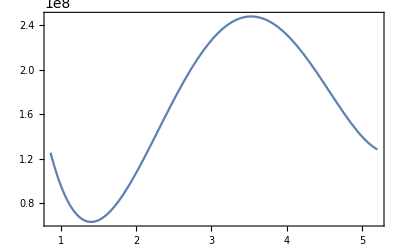

```mathematica
(*s=1,np=1/2,m=0*)
Plot[dProbabTwist1ko[0, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full]
```

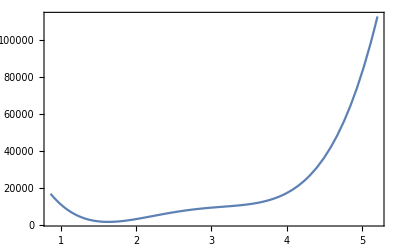

```mathematica
(*s=1,np=1/2,m=-2*)
Plot[dProbabTwist1ko[-2, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full]
```

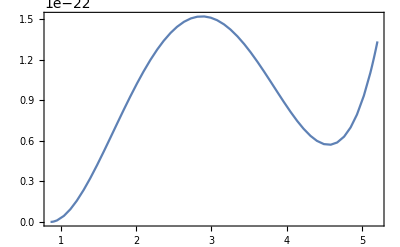
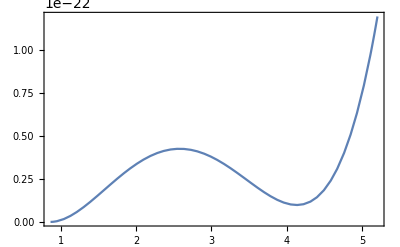
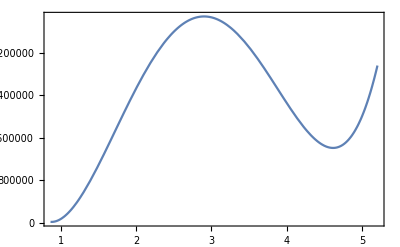
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*s=1,np=1/2,m=-1;-2;1;2*)
{Plot[dProbabTwist1ko[-1, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full],Plot[dProbabTwist1ko[-2, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full], Plot[dProbabTwist1ko[1, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full],Plot[dProbabTwist1ko[2, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*График по np для s=1, ko=3.47/mee, m={-2:2}*)
```

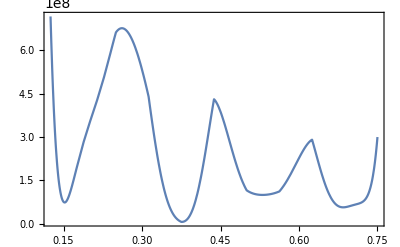

```mathematica
Plot[dProbabTwist1np[0, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full]
```

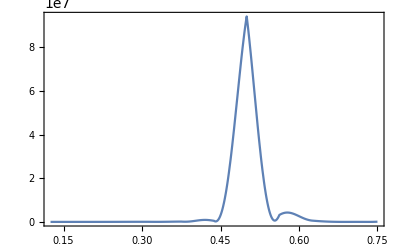

```mathematica
Plot[dProbabTwist1np[-2, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full]
```